## Recurrence Quantification Analysis

An analysis method for dynamical systems.

Flip Phillips
Skidmore College Vision Laboratories
© 2015-9

#### Acknowledgements

• I was introduced to RQA for eye tracking, somewhat skeptically, by Jeff Pelz of RIT.
• The original package was developed with my student Dave ‘CORM’ Jacobs for work on eye tracking trajectory analysis.
• The package was further developed for use by Alison Ord as part of the 2019 Wolfram Summer School. Code contributions from Paul Abbott.

### Notes

Much can be learned from —

Webber Jr, C. L., & Zbilut, J. P. (2005). Recurrence quantification analysis of nonlinear dynamical systems. Tutorials in contemporary nonlinear methods for the behavioral sciences, 94, 26-94. https://www.nsf.gov/pubs/2005/nsf05057/nmbs/chap2.pdf

This chapter is from a collection on the subject of nonlinear methods, Tutorials in contemporary nonlinear methods for the behavioral sciences, written for the NFS and edited by Michael Riley and Guy Van Orden. https://nsf.gov/pubs/2005/nsf05057/nmbs/nmbs.pdf

Guy passed away from pancreatic cancer a few years after I met him. He was a super nice, encouraging, and helpful person. If you use this package and feel the need to pay-it-forward somehow, consider dropping a few bucks to a cancer charity or the NSF or NIH.

## Examples

### Preliminaries

Load the package:

```mathematica
<<RQA`
```

If you’d like to see what is there —

```mathematica
?RQA`*
```

### Data

We use a Henon attractor as example data.

```mathematica
α=1.4;β=0.3;nMax=2000;settle=40;
```

```mathematica
henonxy=
Drop[RecurrenceTable[{x[n+1]==1-α x[n]^2+y[n],
y[n+1]==β x[n],x[0]==0.0,y[0]==0.0},{x,y},{n,1,nMax+settle},DependentVariables->{x,y}],settle];
```

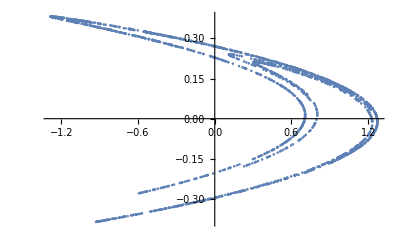

```mathematica
ListPlot[henonxy]
```

### Time Series

The RQA package uses the Wolfram Language TimeSeries as its primary data structure. This is primarily since the analysis our lab has used has been in the time domain. Obviously, RQA is not limited to temporal dynamics, so this is a bit of a compromise that creates a class of parametric function in one variable. Future versions might (well, do in our local stuff) support other parameterizations, multidimensional in nature:

```mathematica
hts=TimeSeries[TemporalData[henonxy,{1,Automatic,1},ValueDimensions->2]]
```

TimeSeries[…]

Let’s use an interesting, 200-wide, window:

```mathematica
tStart=1001;
w=200;
```

```mathematica
hw=TimeSeriesWindow[hts,{tStart,tStart+w-1}]
```

TimeSeries[…]

Make a 1D, x-only version looking at just the changes of the x-variable:

```mathematica
hx=TimeSeries[TemporalData[hw["Values"][[All,1]],{tStart,tStart+w-1,1}]]
```

TimeSeries[…]

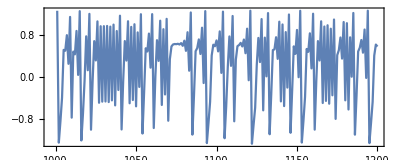

```mathematica
ListLinePlot[hx,Axes->None,Frame->True,AspectRatio->.4]
```

#### Embedding

Embed our data into 3 dimensions with a lag/τ of 1.0:

```mathematica
hxe3=RQAEmbed[hx,3,1.0]
```

TimeSeries[…]

This shows how the x-coordinate jumps back and forth over time but within the pattern of the attractor:

```mathematica
ParametricPlot3D[hxe3[t],{t,1001,1198}]
```

-Graphics3D-

#### Distance Map

An unscaled distance map from the above embedding, using EuclideanDistance as a metric:

```mathematica
dm=RQADistanceMap[hxe3,DistanceFunction->EuclideanDistance];
```

You can use any distance function you’d like. By default, SquaredEuclideanDistance is used.

```mathematica
ArrayPlot[dm,DataReversed->True,PlotLegends->Automatic,FrameTicks->None,ColorFunction->ColorData["Temperature"],ImageSize->500,FrameLabel->{"time","time",None,None}]
```

-Graphics-

The above is a plot of the distances over time. The x and y axes are increasing t from the lower left.

#### Recurrence Map

Here' s a true recurrence map with a distance threshold of 0.03:

```mathematica
ArrayPlot[rm=RQARecurrenceMap[hxe3,0.03,"Rescale"->True,DistanceFunction->EuclideanDistance],DataReversed->True,FrameTicks->None,ImageSize->500]
```

-Graphics-

We can make a nice distance-coded version by multiplying the recurrence map by the distance map. Here, we rescale the distance map to get everything normalized on {0,1} do the right thing, rendering-wise —

```mathematica
ArrayPlot[rm*dm,DataReversed->True,PlotLegends->Automatic,FrameTicks->None,ColorFunctionScaling->True,ColorFunction->ColorData[{"DarkTerrain","Reverse"}]]
```

-Graphics-

Not as visually interesting for this rather sparse map, but, it gets cooler as things get bigger.

### RQA Measurements

#### Recurrence

```mathematica
RQARecurrence[rm]//N
```

0.0167154

#### Determinism

```mathematica
RQADeterminism[rm]//N
```

0.865031

#### Dmax (aka Vmax in earlier work)

```mathematica
RQADmax[rm]
```

12

#### Entropy

```mathematica
RQAEntropy[rm]//N
```

2.54305

#### Trend

```mathematica
RQATrend[rm]//N
```

-3.69311

Note that, right now, I believe the trend calculations are wrong.

#### Laminarity

```mathematica
RQALaminarity[rm]//N
```

0.134969

#### Trapping time

```mathematica
RQATrappingTime[rm,2]//N
```

4.4

```mathematica
RQAVmax[rm]
```

7

```mathematica
RQAChaos[rm]//N
```

0.0833333